Пример 1. За период с 1998 по 2004 гг.известен динамический ряд материалопотока регионального склада. Сделаем прогноз на 2005-2007 г.г.
Исходные данные:

```mathematica
ИсходныеДанные1=TableForm[{{1998,130},{1999,148},{2000,170},{2001,190},{2002,210},{2003,225},{2004,250}}]
```

1998 | 130
1999 | 148
2000 | 170
2001 | 190
2002 | 210
2003 | 225
2004 | 250

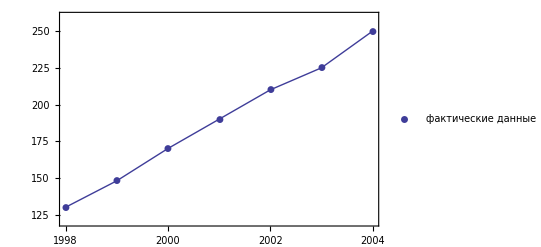

```mathematica
DateListPlot[{130,148,170,190,210,225,250},{1998}, Joined->True,PlotRange->{120,260},PlotLegends->{"фактические данные"}, PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,{130,148,170,190,210,225,250}}]
```

Очевидна линейная тенденция изменения материалопотока. Поэтому связь между указанными признаками может быть описана уравнением:
y_x=a+bx   где y_x — материалопоток регионального склада, усл. ед.;
		x — рассматриваемый период;
		a — товарооборот при нулевом периоде (x=0);
		b — ежегодний прирост.

```mathematica
a=(∑y)/n;
```

```mathematica
a1=Total[{130,148,170,190,210,225,250}]/7
```

189

```mathematica
b=(∑yx)/(∑x^2);
```

```mathematica
b1 = Total[{-3,-2,-1,0,1,2,3}×{130,148,170,190,210,225,250}]/Total[{-3,-2,-1,0,1,2,3}^2]//N
```

19.7857

Тогда уравнение нашей прямой будет следующим, где последующие значения х соответствуют годам 2005, 2006, 2007:

```mathematica
Subscript[y, x]=189+19.7857x;
```

```mathematica
(a1+b1×#)&/@{-3,-2,-1,0,1,2,3,4,5,6}
```

{129.643,149.429,169.214,189.,208.786,228.571,248.357,268.143,287.929,307.714}

Добавим расчетные данные на график:

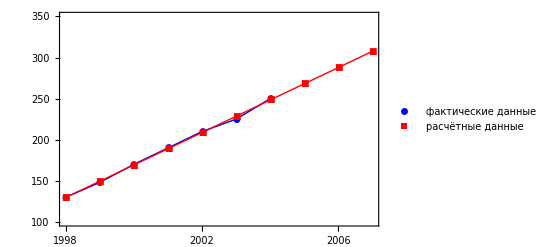

```mathematica
DateListPlot[{{130,148,170,190,210,225,250}, {129.6429,149.42860000000002,169.2143,189.,208.7857,228.57139999999998,248.3571,268.14279999999997,287.9285,307.7142}},{1998}, Joined->True,PlotRange->{100,350},PlotLegends->{"фактические данные","расчётные данные"},PlotStyle->{Blue,Red},PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,{130,148,170,190,210,225,250}}]
```

Пример 2. Если уровни динамического ряда обнаруживают тенденцию роста по геометрической прогрессии, т.е. прирастают на одинаковое число процентов, выравнивание такого ряда следует проводить по показательной кривой: y_x=ab^x. В этом уравнении x — рассматриваемый период, а — начальный уровень ряда (при х=0), b — темп роста за единицу времени.
Техника выравнивания по показательной кривой аналогична технике выравнивания по прямой.

Пример 3. Уравнение параболы второго порядка y_x=a+bx+cx^2. Известен динамический ряд объема перевозок грузов (тыс. тонн) с регионального склада в 1999-2004 г.г. Сделать прогноз.

```mathematica
ИсходныеДанные3=TableForm[{{1999,5398},{2000,5718},{2001,6132},{2002,6885},{2003,7647},{2004,8518}}]
```

1999 | 5398
2000 | 5718
2001 | 6132
2002 | 6885
2003 | 7647
2004 | 8518

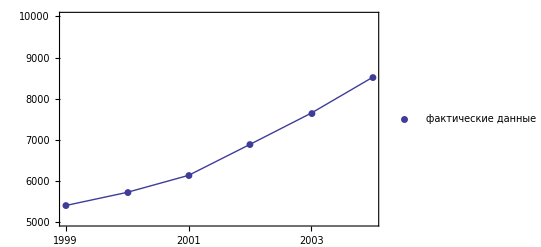

```mathematica
DateListPlot[{5398,5718,6132,6885,7647,8518},{1999}, Joined->True,PlotRange->{5000,10000},PlotLegends->{"фактические данные"}, PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,{5398,5718,6132,6885,7647,8518}}]
```

Тогда:

```mathematica
a = (∑y∑x^4-∑x^2 y∑x^2)/(n∑x^4-∑x^2∑x^2);
```

```mathematica
b=(∑xy)/(∑x^2);
```

```mathematica
c = (n∑x^2 y-∑x^2∑y)/(n∑x^4-∑x^2∑x^2);
```

где пусть:

```mathematica
y3={5398,5718,6132,6885,7647,8518};
```

```mathematica
x3= {-5,-3,-1,1,3,5};
```

```mathematica
n3 = 6;
```

```mathematica
a3=(Total[y3]×Total[x3^4]-Total[(x3^2)×y3]×Total[x3^2])/(n3×Total[x3^4]-Total[x3^2]×Total[x3^2])//N
```

6500.34

```mathematica
b3=(Total[x3×y3])/(Total[x3^2])//N
```

316.286

```mathematica
c3=(n3×Total[(x3^2)×y3]-Total[x3^2]×Total[y3])/(n3×Total[x3^4]-Total[x3^2]×Total[x3^2])//N
```

18.5134

Таким образом, уравнение параболы в нашем примере имеет вид:
y_x =6500.34+316.286x+18.5134x^2 где х 7,9,11 будут 2005,2006,2007 года соответственно.

```mathematica
(a3+b3×#+c3×(#^2))&/@{-5,-3,-1,1,3,5,7,9,11}
```

{5381.75,5718.11,6202.57,6835.14,7615.82,8544.61,9621.5,10846.5,12219.6}

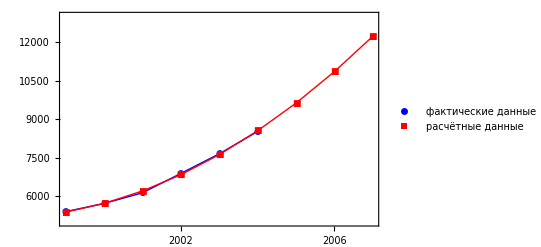

```mathematica
DateListPlot[{{5398,5718,6132,6885,7647,8518},{5381.75,5718.107142857142,6202.571428571428,6835.142857142858,7615.821428571428,8544.607142857143,9621.5,10846.5,12219.607142857143}},{1999}, Joined->True,PlotRange->{5000,13000},PlotLegends->{"фактические данные","расчётные данные"},PlotStyle->{Blue,Red},PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,{5398,5718,6132,6885,7647,8518}}]
```